# Pythagoras Tree

Adam Rumpf, 1/6/2016

## Introduction

A Pythagoras tree is a fractal generated by iteratively by beginning with one square, and then repeatedly stacking two smaller squares on top of every square in the most recent generation, leaning against  each other and meeting at their corner. The relative sizes of the two boxes can be adjusted to yield different shapes of tree.

The main function defined below, pythagorastree[], accepts variable numbers of arguments to generate a Pythagoras tree. If given only an integer, it will generate a wireframe symmetric tree with the specified number of iterations. The optional second argument selects the ratio of the side lengths of the left and right child squares, respectively (so 1 is symmetric, >1 makes left larger, and <1 makes right larger). The third argument is a boolean value to select whether to fillin the boxes (defaults to False for wireframe, while True is solid fill). The fourth argument is a pair of triples specifying the initial and final RGB vectors, respectively, and causes the shading to smoothly fade from one to the other as the generations advance. The fifth argument is a pair of initial and final opacity values, and causes the opacity to smoothly fade from one to the other as the generations advance.

## Code

### Initialization

```mathematica
(* left[tl,len,θ] accepts the coordinates of a top left corner, a length, and an angle, and returns the coordinates of the corners of the left child square. *)
left[tl_,len_,θ_]:={tl,tl+len{Cos[θ],Sin[θ]},tl+len √2{Cos[θ+π/4],Sin[θ+π/4]},tl+len{Cos[θ+π/2],Sin[θ+π/2]},tl};
```

```mathematica
(* right[tr,len,θ] accepts the coordinates of a top right corner, a length, and an angle, and returns the coordinates of the corners of the right child square. *)
right[tr_,len_,θ_]:={tr-len{Cos[θ],Sin[θ]},tr,tr-len{Cos[θ-π/2],Sin[θ-π/2]},tr-len √2{Cos[θ-π/4],Sin[θ-π/4]},tr-len{Cos[θ],Sin[θ]}};
```

```mathematica
(* interpolate[x,y,n] gives a list of n numbers linearly interpolated between x and y. *)
interpolate[x_,y_,n_]:=Table[N[(1-t)x+t y],{t,0,1,1/(n-1)}];
```

```mathematica
(* rgbint[col1,col2,n] gives a list of n colors whose extremes are col1 and col2, with all other elements varying linearly between the two.  The color inputs are triples of RGB values. *)
rgbint[col1_,col2_,n_]:=Table[RGBColor[(1-t)col1[[1]]+t col2[[1]],(1-t)col1[[2]]+t col2[[2]],(1-t)col1[[3]]+t col2[[3]]],{t,0,1,1/(n-1)}];
```

```mathematica
(* pythagorastree[n,r,solid,col,opac] generates an outline Pythagoras tree with n iterations and a ratio between the left- and right-child sizes of r.  solid stores whether the squares should be solid, col stores the starting and ending colors, while opac stores the starting and ending opacities. *)
pythagorastree[n_,r_:1,solid_:False,col_:{{0,0,0},{0,0,0}},opac_:{1,1}]:=Module[{squares,i,old, new,θl,θr,angles,anglesold,lengths,lengthsold,collist,opaclist,g},
(* squares = list of coordinates of each square
i = current layer
old = list of squares from the last iteration (parents)
new = list of newly-generates squares (children)
θ* = * angle
angles = list of all new top edge angles
anglesold = list of all old top endge angles
lengths = list of all new lengths
lengthsold = list of all old lengths
collist = list of colors to use
opaclist = list of opacities to use
g = line or polygon *)
collist=rgbint[col[[1]],col[[2]],n+1];
opaclist=interpolate[opac[[1]],opac[[2]],n+1];
If[solid==True,
g[x_]:=Polygon[x],
g[x_]:=Line[x];
];
squares={collist[[1]],Opacity[opaclist[[1]]],g[{{0,0},{1,0},{1,1},{0,1},{0,0}}]};
θr=ArcTan[r];
θl=π/2-θr;
anglesold={0};
lengthsold={1};
old={{{0,0},{1,0},{1,1},{0,1},{0,0}}};
For[i=1,i≤n,i++,
angles=Table[If[OddQ[k]==True,N[Mod[anglesold[[(k+1)/2]]+θl,2π]],N[Mod[anglesold[[k/2]]-θr,2π]]],{k,1,2^i}];
lengths=Table[If[OddQ[k]==True,N[(r lengthsold[[(k+1)/2]])/(√(r^2+1))],N[lengthsold[[k/2]]/(√(r^2+1))]],{k,1,2^i}];
new=Table[If[OddQ[k]==True,left[old[[(k+1)/2,4]],lengths[[k]],angles[[k]]],right[old[[k/2,3]],lengths[[k]],angles[[k]]]],{k,1,2^i}];
anglesold=angles;
lengthsold=lengths;
old=new;
squares=Join[squares,{collist[[i+1]],Opacity[opaclist[[i+1]]],g[new]}];
];
Graphics[squares]
];
```

### Demonstration

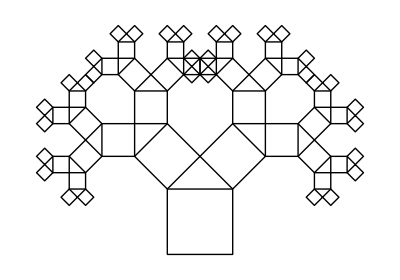

```mathematica
(* Simple Pythagoras tree with 5 generations. *)
pythagorastree[5]
```

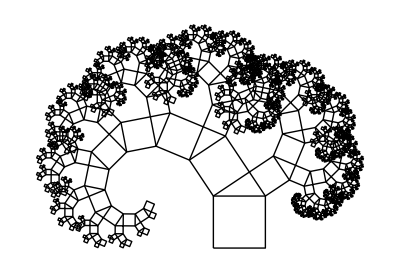

```mathematica
(* Asymmetric Pythagoras tree biased towards left. *)
pythagorastree[10,1.5]
```

```mathematica
(* Play with the side length ratio. *)
Manipulate[pythagorastree[8,r],{{r,1},1/3,3}]
```

```mathematica
(* Fading Pythagoras tree (constant zero vectors specify initial and final colors as black) *)
```

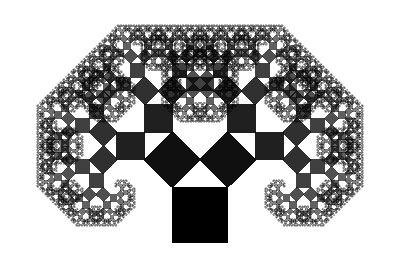

```mathematica
pythagorastree[12,1,True,{{0,0,0},{0,0,0}},{1,0.25}]
```

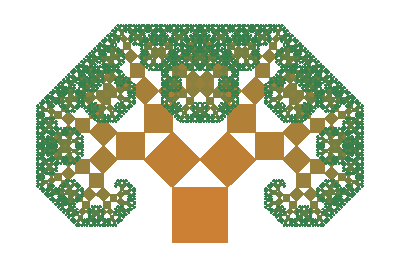

```mathematica
(* Pythagoras tree that fades from brown to green. *)
pythagorastree[12,1,True,{{0.8,0.5,0.2},{0.2,0.5,0.3}}]
```